# CEE-290: Models & Data HOMEWORK 5: BAYESIAN ANALYSIS A Mathematica Implementation Baoxiang Pan ID: 63324929

## 1.MCMC Simulation

1.Random walk Metropolis

```mathematica
RandomWalkMetropolis[pdf_,start_,delta_,times_]:=
Module[{f},
	f[current_]:=Module[{w,new},
		new=current+RandomReal[{-delta,delta}];
		w=Min[1,pdf[new]/pdf[current]];
		If[RandomReal[]<w,new,current]];
	Return[NestList[f,start,times]];
]
```

## II.Test Problem: N(0,1)

2.

N(0,1) is maximized when x=0.

3.

```mathematica
InverseCDF[NormalDistribution[0,1],0.025]
```

-1.95996

```mathematica
InverseCDF[NormalDistribution[0,1],0.975]
```

1.95996

The 95% uncertainty ranges of x is [-1.95996, 1.95996]

4.

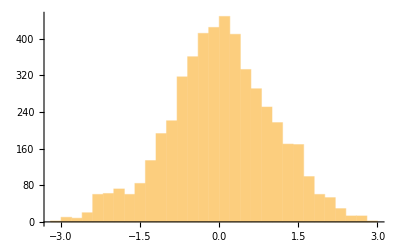

```mathematica
pdf[x_]:=PDF[NormalDistribution[0,1],x];
z=RandomWalkMetropolis[pdf,RandomReal[{-5,5}],0.5,10000];
Histogram[z[[5001;;10000]]]
```

5.

```mathematica
Mean[z[[5001;;10000]]]
```

0.0233427

```mathematica
Sqrt[Variance[z[[5001;;10000]]]]
```

0.989577

6.

6.1,Parametric Method:
Using the samples to fit normal distribution and calculate 95% range with the estimated p.d.f.
Moment Estimation:

```mathematica
μ=Mean[z[[5001;;10000]]];
σ=Variance[z[[5001;;10000]]]*5000/4999;
range={InverseCDF[NormalDistribution[μ,σ],0.025],InverseCDF[NormalDistribution[μ,σ],0.025]}
```

{-1.89636,-1.89636}

Maximum Likelihood Estimation

```mathematica
loglikelihood[mu_,sigma_]:=Plus@@Map[Log[PDF[NormalDistribution[mu,sigma],#]]&,z[[5001;;10000]]];
{μ,σ}=FindArgMax[loglikelihood[x,y],{{x,0.1},{y,0.9}}];
range={InverseCDF[NormalDistribution[μ,σ],0.025],InverseCDF[NormalDistribution[μ,σ],0.025]}
```

{-1.916,-1.916}

6.2, Non-parametric Method:
Sort the samples to find the 2.5% and 97.5% quantile.

```mathematica
zsort=Sort[z[[5001;;10000]]];
range={zsort[[Floor[0.025*Length[zsort]]]],zsort[[Floor[0.975*Length[zsort]]]]}
```

{-2.12406,1.93477}

7.

The 2.5% quantile is -2.12406; the 97.5% quantile is 1.83477.

8.

Burn in.

9.

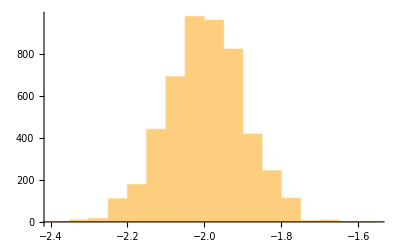

```mathematica
pdf[x_]:=PDF[NormalDistribution[-2,0.1],x];
z2=RandomWalkMetropolis[pdf,RandomReal[{-5,5}],0.5,10000];
Histogram[z2[[5001;;10000]]]
```

10.

```mathematica
Mean[z2[[5001;;10000]]]
```

-1.99734

```mathematica
Sqrt[Variance[z2[[5001;;10000]]]]
```

0.100358

11.

```mathematica
InverseCDF[NormalDistribution[-2,0.1],0.025]
```

-2.196

```mathematica
InverseCDF[NormalDistribution[-2,0.1],0.975]
```

-1.804

The 95% uncertainty ranges of x is [-2.196, 1.804].

12.

13.

## III.Test Problem: Bimodal Normal Distribution

14.

```mathematica
pdf[x_]:=1/3*PDF[NormalDistribution[-5,1],x]+2/3*PDF[NormalDistribution[5,1],x];
FindMaximum[pdf[x],{x,4,98},AccuracyGoal->10,PrecisionGoal->10]
```

{0.265962,{x→5.}}

p(x|μ1,σ1,μ2,σ2)is maximized at x=5, the p.d.f. is 0.265962.

15.

16.

Now lets apply your RWM algorithm to Equation (4). Please use as proposal distribution, q = U[−1/2,1/2], randomly initialize the starting point of your Markov chain between, x ∈ [−10,10], and create T = 25, 000 samples of x. Discard the first 15, 000 samples of your chain (also called burn-in) and then answer the following questions.

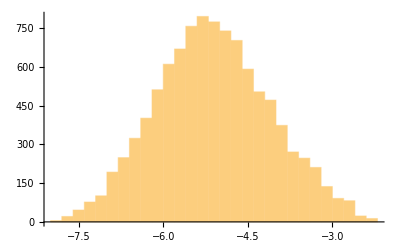

```mathematica
z=RandomWalkMetropolis[pdf,RandomReal[{-10,10}],0.5,25000];
Histogram[z[[15001;;25000]]]
```

17.

```mathematica
Mean[z[[5001;;10000]]]
```

-4.9224

```mathematica
Variance[z[[5001;;10000]]]
```

1.16267

18.

No.

19(1).

## IV.Multiple Chain Methods: DE-MC and DREAM

19(2).

20.

21.

22.

## V.Real-world Study - Hydrologic Modelling

23.

24.

25.

26.

27.

```mathematica
Plus@@{1,2,3}
```

6